```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
Print["Runs in the list: ",runNum={12681,12684,12687,12688,12689,12690,12691,12692}];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: {12681,12684,12687,12688,12689,12690,12691,12692}

Size: 8

```mathematica
metadata1=Table[{},{k,1,Round[runn/2]}];
metadata2=Table[0,{k,1,Round[runn/2]}];
ftdatud=Table[{},{k,1,Round[runn/2]}];
ptdatud=Table[0,{k,1,Round[runn/2]}];
fit1=Table[0,{k,1,Round[runn/2]}];
ftdatudmon=Table[{},{k,1,Round[runn/2]}];
ptdatudmon=Table[0,{k,1,Round[runn/2]}];
fit2=Table[0,{k,1,Round[runn/2]}];
For[i=1,i≤Round[runn/2],i++,
Print["Starting with Run # : ",runNum[[(2i)-1]]," & ",runNum[[(2i)]]];
metadata1[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)-1]],10,6],"\\",IntegerString[runNum[[(2i)-1]],10,6],"_Meta3.edm"],metaStructure2];
metadata2[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)]],10,6],"\\",IntegerString[runNum[[(2i)]],10,6],"_Meta3.edm"],metaStructure2];
maxCy=metadata1[[i]][[-1]][[2]];
(*UD*)
Print["Fit1:UD"];
tab=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/1000,(Sqrt[metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]]])/1000}},{k,1,maxCy}];
ptdatud[[i]]=AppendTo[tab,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/1000,(Sqrt[metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]]])/1000}}];
If[i==2,ptdatud[[i]]=Delete[ptdatud[[i]],4]];
If[i==3,ptdatud[[i]]=Delete[ptdatud[[i]],3]];
ftdatud[[i]]=Transpose[{ptdatud[[i]][[;;,1]],ptdatud[[i]][[;;,2]][[;;,1]]}];
Print[fit1[[i]]=NonlinearModelFit[ftdatud[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
(*UD/Mon*)
Print["Fit2:UD/Mon"];
tab2=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/metadata1[[i]][[k]][[30]],(Sqrt[metadata1[[i]][[k]][[27]]]+Sqrt[metadata1[[i]][[k]][[28]]])/metadata1[[i]][[k]][[30]]}},{k,1,maxCy}];
ptdatudmon[[i]]=AppendTo[tab2,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/metadata2[[i]][[1]][[30]],(Sqrt[metadata2[[i]][[1]][[27]]]+Sqrt[metadata2[[i]][[1]][[28]]])/metadata2[[i]][[1]][[30]]}}];
If[i==2,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],4]];
If[i==3,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],3]];
ftdatudmon[[i]]=Transpose[{ptdatudmon[[i]][[;;,1]],ptdatudmon[[i]][[;;,2]][[;;,1]]}];
Print[fit2[[i]]=NonlinearModelFit[ftdatudmon[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
Print["---"];
];
(*
{aa,bb,cc,dd,ee};
{{aa,1},{bb,1},{cc,-1},{dd,1},{ee,-1}}
*)
```

Starting with Run # : 12681 & 12684

Fit1:UD

FittedModel[1.32355+173.412 ⅇ^(-1.03538 t)+16.4029 ⅇ^(-0.00603346 t)]

Fit2:UD/Mon

FittedModel[0.00622475+27.65 ⅇ^(-0.697654 t)+0.0759593 ⅇ^(-0.00619004 t)]

---

Starting with Run # : 12687 & 12688

Fit1:UD

FittedModel[10.8417-13.6656 ⅇ^(-2.15551 t)+91.8044 ⅇ^(-0.010548 t)]

Fit2:UD/Mon

FittedModel[0.00972756-6.17046 ⅇ^(-0.531363 t)+0.0960547 ⅇ^(-0.00758587 t)]

---

Starting with Run # : 12689 & 12690

Fit1:UD

FittedModel[7.26364+28.4414 ⅇ^(-4.65532 t)+79.8589 ⅇ^(-0.00729495 t)]

Fit2:UD/Mon

FittedModel[0.00840624+29.5281 ⅇ^(-1.33283 t)+0.0894173 ⅇ^(-0.00657062 t)]

---

Starting with Run # : 12691 & 12692

Fit1:UD

FittedModel[5.0024+517.598 ⅇ^(-1.42655 t)+72.3616 ⅇ^(-0.0061986 t)]

Fit2:UD/Mon

FittedModel[0.0122227+6.07127 ⅇ^(-1.01924 t)+0.0957033 ⅇ^(-0.0082354 t)]

---

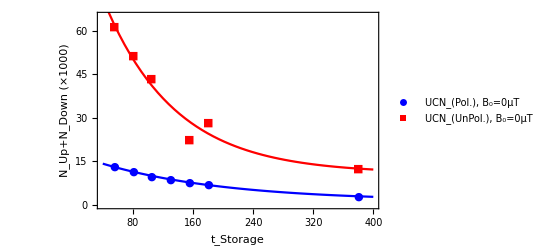

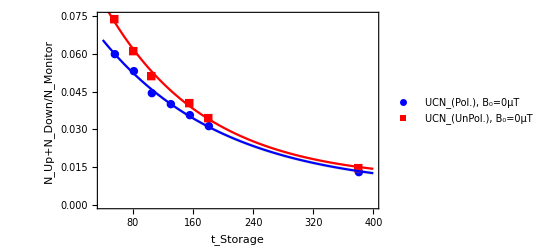

```mathematica
Show[{
EDAListPlot[ptdatud[[1]],ptdatud[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down (×1000)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[1]][t],fit1[[2]][t],fit1[[1]][t]+ptdatud[[1]][[1]][[2]][[2]],fit1[[1]][t]-ptdatud[[1]][[1]][[2]][[2]],fit1[[2]][t]+ptdatud[[2]][[1]][[2]][[2]],fit1[[2]][t]-ptdatud[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[1]],ptdatudmon[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[1]][t],fit2[[2]][t],fit2[[1]][t]+ptdatudmon[[1]][[1]][[2]][[2]],fit2[[1]][t]-ptdatudmon[[1]][[1]][[2]][[2]],fit2[[2]][t]+ptdatudmon[[2]][[1]][[2]][[2]],fit2[[2]][t]-ptdatudmon[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

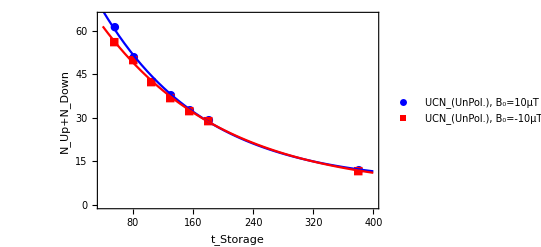

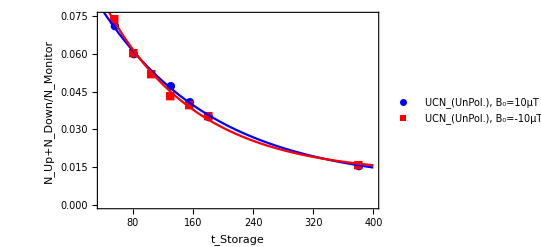

```mathematica
Show[{
EDAListPlot[ptdatud[[3]],ptdatud[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[3]][t],fit1[[4]][t],fit1[[3]][t]+ptdatud[[3]][[1]][[2]][[2]],fit1[[3]][t]-ptdatud[[3]][[1]][[2]][[2]],fit1[[4]][t]+ptdatud[[4]][[1]][[2]][[2]],fit1[[4]][t]-ptdatud[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[3]],ptdatudmon[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[3]][t],fit2[[4]][t],fit2[[3]][t]+ptdatudmon[[3]][[1]][[2]][[2]],fit2[[3]][t]-ptdatudmon[[3]][[1]][[2]][[2]],fit2[[4]][t]+ptdatudmon[[4]][[1]][[2]][[2]],fit2[[4]][t]-ptdatudmon[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

```mathematica
ptdatudmon[[2]]
ptdatudmon[[3]]
ptdatudmon[[4]]
```

{{55,{0.0739628,0.000422606}},{80,{0.0614265,0.000383263}},{105,{0.051403,0.000349193}},{155,{0.0406109,0.000381609}},{180,{0.0346558,0.00029071}},{380,{0.014797,0.000186751}}}

{{55,{0.0712409,0.000406908}},{80,{0.0600757,0.000376268}},{130,{0.0474324,0.000343512}},{155,{0.0411074,0.000320581}},{180,{0.035053,0.000289089}},{380,{0.015804,0.000203152}}}

{{55,{0.0741104,0.000442673}},{80,{0.0606785,0.00038343}},{105,{0.0520993,0.000357561}},{130,{0.0435714,0.000321261}},{155,{0.0398941,0.000312909}},{180,{0.0353641,0.000292852}},{380,{0.015945,0.000207199}}}

```mathematica
superdat={};
superdat=AppendTo[superdat,{ptdatudmon[[2]][[1]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[1]][[2]][[1]],ptdatudmon[[2]][[1]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[1]][[2]][[1]],ptdatudmon[[3]][[1]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[1]][[2]][[1]],ptdatudmon[[4]][[1]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[2]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[2]][[2]][[1]],ptdatudmon[[2]][[2]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[2]][[2]][[1]],ptdatudmon[[3]][[2]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[2]][[2]][[1]],ptdatudmon[[4]][[2]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[3]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[3]][[2]][[1]],ptdatudmon[[2]][[3]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[3]][[2]][[1]],ptdatudmon[[4]][[3]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[3]][[3]][[1]],Mean[{PlusMinus[ptdatudmon[[3]][[3]][[2]][[1]],ptdatudmon[[3]][[3]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[4]][[2]][[1]],ptdatudmon[[4]][[4]][[2]][[2]]]}]}];
superdat=AppendTo[superdat,{ptdatudmon[[2]][[4]][[1]],Mean[{PlusMinus[ptdatudmon[[2]][[4]][[2]][[1]],ptdatudmon[[2]][[4]][[2]][[2]]],PlusMinus[ptdatudmon[[3]][[4]][[2]][[1]],ptdatudmon[[3]][[4]][[2]][[2]]],PlusMinus[ptdatudmon[[4]][[5]][[2]][[1]],ptdatudmon[[4]][[5]][[2]][[2]]]}]}];
AccountingForm[TableForm[SetPrecision[superdat,10]]]
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["Runs in the list: ",runNum2=descdat[[;;15,4]]];
Print["Storage time in the list: ",ts2=descdat[[;;15,7]]];
Print["Size: ",runn2=Dimensions[runNum2][[1]]];
For[runi=1,runi≤runn2,runi++,
metadatascr=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[runi]],10,6],"\\",IntegerString[runNum2[[runi]],10,6],"_Meta5-2.dat"],metaStructure2];
superdat=AppendTo[superdat,{ts2[[runi]],Mean[Table[(PlusMinus[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]]),Sqrt[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]])]])/PlusMinus[(metadatascr[[k]][[30]]),Sqrt[(metadatascr[[k]][[30]])]],{k,1,Dimensions[metadatascr][[1]]}]]}];
];
superdat=Sort[superdat,#1[[1]]<#2[[1]]&];
expsuperdat=AccountingForm[TableForm[SetPrecision[superdat,10]]]
```

55.00000000 | 0.07310000000±0.0002500000000
80.00000000 | 0.06073000000±0.0002200000000
105.0000000 | 0.05175000000±0.0002500000000
130.0000000 | 0.04550000000±0.0002300000000
155.0000000 | 0.04054000000±0.0002000000000

Runs in the list: {12693,12695,12697,12704,12707,12770,12771,12772,12773,12774,12775,12778,12779,12780,12781}

Storage time in the list: {180,180,180,380,380,200,220,240,260,280,300,320,340,360,300}

Size: 15

55.00000000 | 0.07310000000±0.0002500000000
80.00000000 | 0.06073000000±0.0002200000000
105.0000000 | 0.05175000000±0.0002500000000
130.0000000 | 0.04550000000±0.0002300000000
155.0000000 | 0.04054000000±0.0002000000000
180.0000000 | 0.03398720000±0.000009100000000
180.0000000 | 0.03414900000±0.00001100000000
180.0000000 | 0.03424300000±0.00001700000000
200.0000000 | 0.03672700000±0.00004000000000
220.0000000 | 0.03359300000±0.00003800000000
240.0000000 | 0.03062900000±0.00003800000000
260.0000000 | 0.02809700000±0.00004000000000
280.0000000 | 0.02584600000±0.00004600000000
300.0000000 | 0.02281700000±0.00007400000000
300.0000000 | 0.02516300000±0.00008000000000
320.0000000 | 0.02162700000±0.00003100000000
340.0000000 | 0.01977000000±0.00003000000000
360.0000000 | 0.01849400000±0.00003600000000
380.0000000 | 0.01437520000±0.000005400000000
380.0000000 | 0.01462490000±0.000005400000000

```mathematica
superdat2={};
gaps={1,1,1,1,1,3,1,1,1,1,1,2,1,1,1,2};
Total[gaps]==Dimensions[superdat][[1]]
For[j=1,j≤Dimensions[gaps][[1]],j++,
superdat2=AppendTo[superdat2,Mean[Table[superdat[[j2]],{j2,Total[gaps[[1;;j]]]+1-gaps[[j]],Total[gaps[[1;;j]]]}]]];
];
expsuperdat2=AccountingForm[TableForm[SetPrecision[superdat2,10]]];
superdat3=superdat2+Table[{23,PlusMinus[0,.00004]},{k,1,Dimensions[superdat2][[1]]}];
expsuperdat3=AccountingForm[TableForm[SetPrecision[superdat3,10]]]
Export["expsuperdat2.dat",superdat3]
```

True

78.00000000 | 0.07310000000±0.0002500000000
103.0000000 | 0.06073000000±0.0002200000000
128.0000000 | 0.05175000000±0.0002500000000
153.0000000 | 0.04550000000±0.0002300000000
178.0000000 | 0.04054000000±0.0002000000000
203.0000000 | 0.03412600000±0.00004100000000
223.0000000 | 0.03672700000±0.00005700000000
243.0000000 | 0.03359300000±0.00005500000000
263.0000000 | 0.03062900000±0.00005500000000
283.0000000 | 0.02809700000±0.00005700000000
303.0000000 | 0.02584600000±0.00006100000000
323.0000000 | 0.02399000000±0.00006800000000
343.0000000 | 0.02162700000±0.00005100000000
363.0000000 | 0.01977000000±0.00005000000000
383.0000000 | 0.01849400000±0.00005400000000
403.0000000 | 0.01450000000±0.00004000000000

expsuperdat2.dat

FittedModel[0.00885333-106.304 ⅇ^(-0.872619 t)+0.112341 ⅇ^(-0.00733609 t)]

FittedModel[0.00242588-104.6 ⅇ^(-6.41881 t)+0.0994643 ⅇ^(-0.00477772 t)]

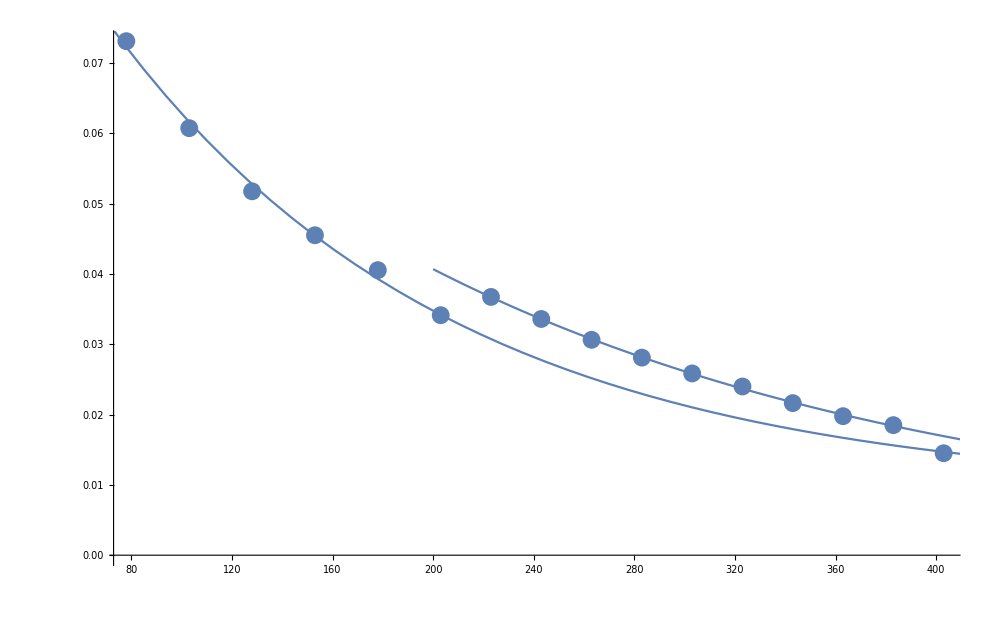

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ptsuperdat3=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,Dimensions[superdat3][[1]]}];
ftsuperdat3=Table[{superdat3[[k]][[1]],superdat3[[k]][[2]][[1]]},{k,1,Dimensions[superdat3][[1]]}];
Print[nlm0=NonlinearModelFit[Join[ftsuperdat3[[1;;6]],{ftsuperdat3[[16]]}],(aa+bb Exp[t cc]+dd Exp[t ee]),{{aa,0.01},{bb,1},{cc,-.1},{dd,1},{ee,-.1}},t,Method->NMinimize]]
Print[nlm01=NonlinearModelFit[ftsuperdat3[[7;;15]],(aa+bb Exp[t cc]+dd Exp[t ee]),{{aa,0.01},{bb,1},{cc,-.1},{dd,1},{ee,-.1}},t,Method->NMinimize]]
Show[{EDAListPlot[ptsuperdat3,ImageSize->1000],Plot[nlm0[xx],{xx,10,420}],Plot[nlm01[xx],{xx,200,420}]}]
nlm00=Interpolation[Join[ftsuperdat3[[1;;6]],{ftsuperdat3[[16]]}]]
nlm001=Interpolation[ftsuperdat3[[7;;15]]]
rat[x_]:=nlm0[x]/nlm01[x];
rat2[x_]:=nlm00[x]/nlm001[x];
rat3[x_]:=nlm0[x]/ftsuperdat3[[7;;15,2]];
```

{{78,{0.0731,0.00025}},{103,{0.06073,0.00022}},{128,{0.05175,0.00025}},{153,{0.0455,0.00023}},{178,{0.04054,0.0002}},{203,{0.034126,0.000041}},{223,{0.0307338,0.0000476986}},{243,{0.0277479,0.0000454301}},{263,{0.0251694,0.0000451963}},{283,{0.0229428,0.0000465438}},{303,{0.0210201,0.0000496102}},{323,{0.0193598,0.0000548755}},{343,{0.017926,0.0000422724}},{363,{0.0166879,0.0000422051}},{383,{0.0156187,0.0000456046}},{403,{0.0146955,0.00004}}}

{{78,0.0731},{103,0.06073},{128,0.05175},{153,0.0455},{178,0.04054},{203,0.034126},{223,0.0307338},{243,0.0277479},{263,0.0251694},{283,0.0229428},{303,0.0210201},{323,0.0193598},{343,0.017926},{363,0.0166879},{383,0.0156187},{403,0.0146955}}

FittedModel[0.032353+0.2 ⅇ^(-10. t)]

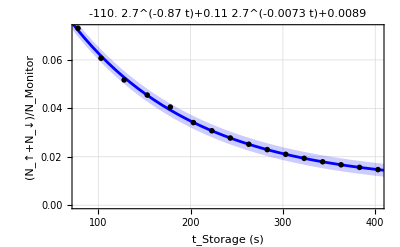

78.00 | 0.07310±0.0002500
103.0 | 0.06073±0.0002200
128.0 | 0.05175±0.0002500
153.0 | 0.04550±0.0002300
178.0 | 0.04054±0.0002000
203.0 | 0.03413±0.00004100
223.0 | 0.03073±0.00004770
243.0 | 0.02775±0.00004543
263.0 | 0.02517±0.00004520
283.0 | 0.02294±0.00004654
303.0 | 0.02102±0.00004961
323.0 | 0.01936±0.00005488
343.0 | 0.01793±0.00004227
363.0 | 0.01669±0.00004221
383.0 | 0.01562±0.00004560
403.0 | 0.01470±0.00004000

expsuperdat3.dat

```mathematica
ptseries1=Join[Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,6}],Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]]*nlm0[superdat3[[k]][[1]]]/superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,16,16}]];
ptseries2=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}*HeavisidePi[(superdat3[[k]][[1]]-313)/200]*rat3[superdat3[[k]][[1]]][[k-6]]},{k,7,15}];
ftseries1=Transpose[{ptseries1[[;;,1]],ptseries1[[;;,2]][[;;,1]]}];
ftseries2=Transpose[{ptseries2[[;;,1]],ptseries2[[;;,2]][[;;,1]]}];
ptallseries=Join[ptseries1,ptseries2];
ptallseries=Sort[ptallseries,#1[[1]]<#2[[1]]&]
ftallseries=Join[ftseries1,ftseries2];
ftallseries=Sort[ftallseries,#1[[1]]<#2[[1]]&]
errallseries=Table[ptallseries[[k]][[2]][[2]],{k,1,Dimensions[ptallseries][[1]]}];
Print[nlm2=NonlinearModelFit[ftallseries,(aa+bb Exp[t/cc]+dd Exp[t/ee]),{{aa,0.01},{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
Show[{
EDAListPlot[ptallseries,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel->SetPrecision[nlm0["BestFit"],2],PlotMarkers->{Red,Medium}],
Plot[{nlm0[xx],nlm0[xx]+nlm0["ParameterErrors"][[1]],nlm0[xx]-nlm0["ParameterErrors"][[1]]},{xx,10,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
AccountingForm[TableForm[SetPrecision[Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}],4]]]
Export["expsuperdat3.dat",Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}]]
```

FittedModel[0.00896845-3.07715 ⅇ^(-0.471693 t)+0.112419 ⅇ^(-0.00736424 t)]

Sigmas: {3.3418,-4.05074,-4.06994,0.423586,6.31954,-1.31196,0.141718,0.0155074,-0.132153,-0.27907,-0.405692,-0.496052,-0.807881,-0.967394,-1.03485,-1.33018}

| DF | SS | MS
Model | 5 | 0.0213347 | 0.00426695
Error | 11 | 4.14656×10^-6 | 3.7696×10^-7
Uncorrected Total | 16 | 0.0213389 | 
Corrected Total | 15 | 0.00459143 |

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.00896845 | 0.00074776 | 11.9938 | 1.16953×10^-7
bb | -3.07715 | 2.93174×10^-19 | -1.0496×10^19 | 7.37554×10^-205
cc | -0.471693 | 9.39612×10^-17 | -5.02009×10^15 | 2.46164×10^-168
dd | 0.112419 | 0.00168433 | 66.7442 | 1.05941×10^-15
ee | -0.00736424 | 0.000232129 | -31.7248 | 3.62824×10^-12

AdjustedRSquared | 0.999717
AIC | -184.252
BIC | -179.616
RSquared | 0.999806

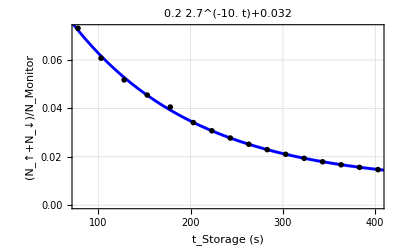

```mathematica
ini=1;
fin=16;
errallseries2=errallseries[[ini;;fin]];
ptallseries2=ptallseries[[ini;;fin]];
ftallseries2=ftallseries[[ini;;fin]];
Print[nlm22=NonlinearModelFit[ftallseries2,(aa+bb Exp[t cc]+dd Exp[t ee]),{{aa,0.01},{bb,1},{cc,-.1},{dd,1},{ee,-.1}},t,Method->NMinimize]];
Print["Sigmas: ",(nlm22["FitResiduals"]/errallseries2)]
nlm22["ANOVATable"]
nlm22["ParameterTable"]
Grid[Transpose[{#,nlm22[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[ptallseries2,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel->SetPrecision[nlm2["BestFit"],2],PlotMarkers->{Red,Medium}],
Plot[{nlm22[xx],nlm22[xx]+nlm22["ParameterErrors"][[1]],nlm22[xx]-nlm22["ParameterErrors"][[1]]},{xx,10,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
```

## Cu-Preliminary

```mathematica
newruns={13013,13015};
newdat={};
newts={10,40,70,100,130,160,200,230,260,290,320,350,380}+23;
Dimensions[newruns][[1]]
For[i=1,i≤Dimensions[newruns][[1]],i++,
newdat=Join[newdat,ReadList[StringJoin[ScrDir,"\\",IntegerString[newruns[[i]],10,6],"_Meta3.edm"],metaStructure2]];
];
Dimensions[newdat][[1]]
ptnewdat=Table[{newts[[k]],{2(newdat[[k]][[27]]+newdat[[k]][[28]])/newdat[[k]][[30]],(Sqrt[newdat[[k]][[27]]]+Sqrt[newdat[[k]][[28]]])/newdat[[k]][[30]]}},{k,1,Dimensions[newdat][[1]]}]
ftnewdat=Table[{newts[[k]],2(newdat[[k]][[27]]+newdat[[k]][[28]])/newdat[[k]][[30]]},{k,1,Dimensions[newdat][[1]]}]
```

2

13

{{33,{0.152285,0.000489667}},{63,{0.115681,0.000424808}},{93,{0.0926913,0.000382308}},{123,{0.0780776,0.000350415}},{153,{0.0649736,0.000319115}},{183,{0.0569987,0.000301303}},{223,{0.0458028,0.00026619}},{253,{0.0402424,0.000253251}},{283,{0.0349287,0.000232803}},{313,{0.0302981,0.000215622}},{343,{0.0280638,0.000211323}},{373,{0.0239452,0.000194427}},{403,{0.0208945,0.000179632}}}

{{33,0.152285},{63,0.115681},{93,0.0926913},{123,0.0780776},{153,0.0649736},{183,0.0569987},{223,0.0458028},{253,0.0402424},{283,0.0349287},{313,0.0302981},{343,0.0280638},{373,0.0239452},{403,0.0208945}}

FittedModel[0.00654004+0.0886878 ⅇ^(-0.0296859 t)+0.134792 ⅇ^(-0.00548997 t)]

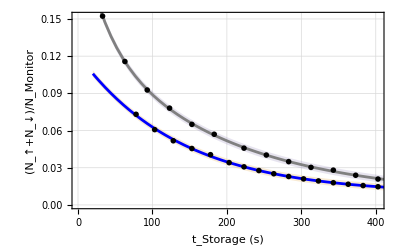

33.00 | 0.1523±0.0004897
63.00 | 0.1157±0.0004248
93.00 | 0.09269±0.0003823
123.0 | 0.07808±0.0003504
153.0 | 0.06497±0.0003191
183.0 | 0.05700±0.0003013
223.0 | 0.04580±0.0002662
253.0 | 0.04024±0.0002533
283.0 | 0.03493±0.0002328
313.0 | 0.03030±0.0002156
343.0 | 0.02806±0.0002113
373.0 | 0.02395±0.0001944
403.0 | 0.02089±0.0001796

```mathematica
Print[nlmnew=NonlinearModelFit[ftnewdat,(aa+bb Exp[t cc]+dd Exp[t ee]),{{aa,0.01},{bb,1},{cc,-.1},{dd,1},{ee,-.1}},t,Method->NMinimize]]
Show[{
EDAListPlot[ptallseries,ptnewdat,PlotLegends->{"Al-Elect.","Cu-Elect."},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{{Red,Medium},{Pink,Medium}}],
Plot[{nlm0[xx],nlm0[xx]+nlm0["ParameterErrors"][[1]],nlm0[xx]-nlm0["ParameterErrors"][[1]],nlmnew[xx],nlmnew[xx]+nlmnew["ParameterErrors"][[1]],nlmnew[xx]-nlmnew["ParameterErrors"][[1]]},{xx,20,420},Filling->{{2->{3}},{5->{6}}},FillingStyle->{{Opacity[.5],Blue},{Opacity[.5],Gray}},PlotStyle->{{Blue,Thickness[.005]},None,None,{Gray,Thickness[.005]},None,None}]
}]
AccountingForm[TableForm[SetPrecision[Table[{ptnewdat[[k]][[1]],PlusMinus[ptnewdat[[k]][[2]][[1]],ptnewdat[[k]][[2]][[2]]]},{k,1,Dimensions[ptnewdat][[1]]}],4]]]
```

```mathematica
Export["expsuperdat_cu3.dat",Table[{ptnewdat[[k]][[1]],PlusMinus[ptnewdat[[k]][[2]][[1]],ptnewdat[[k]][[2]][[2]]]},{k,1,Dimensions[ptnewdat][[1]]}]]
```

expsuperdat_cu3.dat

## Best exponentials

```mathematica
(***)
ini=1;
fin=16;
errallseries3=errallseries[[ini;;fin]];
ptallseries3=ptallseries[[ini;;fin]];
ftallseries3=ftallseries[[ini;;fin]];
stt=50;
endt=2000;
scnftst=-N[1/(stt/Log[2])]
scnend=-N[1/(endt/Log[2])]
numsamples=500;
scnint=Abs[scnend-scnftst]/numsamples;
dimcctvals=Dimensions[Table[cct,{cct,scnftst,scnend,scnint}]][[1]]
parameters=Array[a,{dimcctvals}];
variables=Array[x,{dimcctvals}];
guess=Table[1,{k,1,dimcctvals}];
bbini=1/RandomReal[{1/scnftst,1/scnend},{numsamples+1}];
bb=Sort[bbini,#1>#2&];
f[x_,a_]:=a.Exp[x bb];
nlmfitchk=NonlinearModelFit[ftallseries3,f[xx,parameters],Transpose[{parameters,guess}],xx];
Print["Full Chi^2, basechi2 = ",basechi2=Total[(nlmfitchk["FitResiduals"]/errallseries3)^2]];
nlmfitchktab=ParallelTable[Total[(NonlinearModelFit[ftallseries3,f[xx,parameters]-f[xx,Table[If[k==kk,parameters[[k]],0],{k,1,dimcctvals}]],Transpose[{parameters,guess}],xx]["FitResiduals"]/errallseries3)^2],{kk,1,dimcctvals}];
```

-0.0138629

-0.000346574

501

Full Chi^2, basechi2 = 126.267

$Aborted

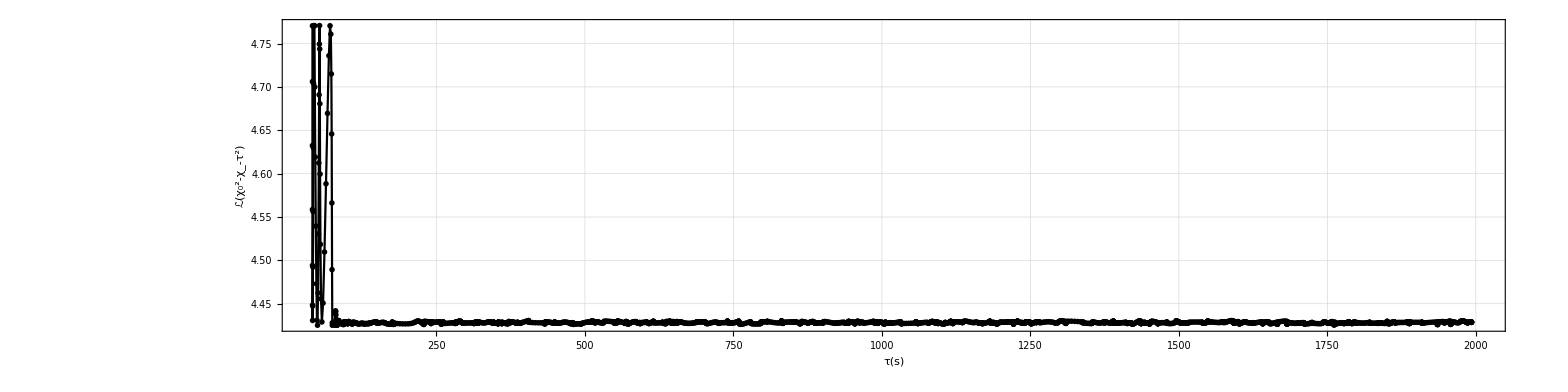

mTau_Laplace.dat

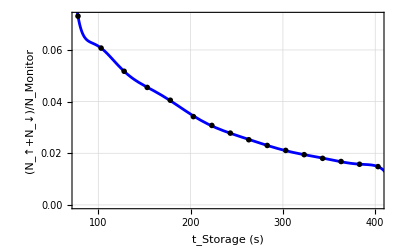

```mathematica
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
ptnlmfitchktab=Table[{-Log[2]/bb[[k]],Log[nlmfitchktab[[k]]]},{k,1,dimcctvals}];
ListLinePlot[ptnlmfitchktab,GridLines->Automatic,PlotRange->{{stt-10,endt+10},Full},Frame->True,FrameStyle->Thickness[.002],PlotStyle->Black,FrameLabel->{"τ(s)","ℒ(χ_0^2-χ_-τ^2)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->2000,AspectRatio->1/4,PlotMarkers->{Red,Small},InterpolationOrder->3]
Export["mTau_Laplace.dat",ptnlmfitchktab]
Show[{
EDAListPlot[ptallseries2,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Red,Medium}],
Plot[nlmfitchk[xx],{xx,10,420},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]}}]
}]
```

```mathematica
kk=2;
f[xx,parameters]-f[xx,Table[If[k==kk,parameters[[k]],0],{k,1,dimcctvals}]]
NonlinearModelFit[ftallseries3,f[xx,parameters]-f[xx,Table[If[k==kk,parameters[[k]],0],{k,1,dimcctvals}]],Transpose[{parameters,guess}],xx]["FitResiduals"]
```

ⅇ^(-0.0691768 xx) a[1]+ⅇ^(-0.0689009 xx) a[3]+ⅇ^(-0.068763 xx) a[4]+ⅇ^(-0.068625 xx) a[5]+ⅇ^(-0.0684871 xx) a[6]+ⅇ^(-0.0683492 xx) a[7]+ⅇ^(-0.0682112 xx) a[8]+ⅇ^(-0.0680733 xx) a[9]+ⅇ^(-0.0679354 xx) a[10]+ⅇ^(-0.0677974 xx) a[11]+ⅇ^(-0.0676595 xx) a[12]+ⅇ^(-0.0675215 xx) a[13]+ⅇ^(-0.0673836 xx) a[14]+ⅇ^(-0.0672457 xx) a[15]+ⅇ^(-0.0671077 xx) a[16]+ⅇ^(-0.0669698 xx) a[17]+ⅇ^(-0.0668319 xx) a[18]+ⅇ^(-0.0666939 xx) a[19]+ⅇ^(-0.066556 xx) a[20]+ⅇ^(-0.0664181 xx) a[21]+ⅇ^(-0.0662801 xx) a[22]+ⅇ^(-0.0661422 xx) a[23]+ⅇ^(-0.0660042 xx) a[24]+ⅇ^(-0.0658663 xx) a[25]+ⅇ^(-0.0657284 xx) a[26]+ⅇ^(-0.0655904 xx) a[27]+ⅇ^(-0.0654525 xx) a[28]+ⅇ^(-0.0653146 xx) a[29]+ⅇ^(-0.0651766 xx) a[30]+ⅇ^(-0.0650387 xx) a[31]+ⅇ^(-0.0649008 xx) a[32]+ⅇ^(-0.0647628 xx) a[33]+ⅇ^(-0.0646249 xx) a[34]+ⅇ^(-0.0644869 xx) a[35]+ⅇ^(-0.064349 xx) a[36]+ⅇ^(-0.0642111 xx) a[37]+ⅇ^(-0.0640731 xx) a[38]+ⅇ^(-0.0639352 xx) a[39]+ⅇ^(-0.0637973 xx) a[40]+ⅇ^(-0.0636593 xx) a[41]+ⅇ^(-0.0635214 xx) a[42]+ⅇ^(-0.0633835 xx) a[43]+ⅇ^(-0.0632455 xx) a[44]+ⅇ^(-0.0631076 xx) a[45]+ⅇ^(-0.0629696 xx) a[46]+ⅇ^(-0.0628317 xx) a[47]+ⅇ^(-0.0626938 xx) a[48]+ⅇ^(-0.0625558 xx) a[49]+ⅇ^(-0.0624179 xx) a[50]+ⅇ^(-0.06228 xx) a[51]+ⅇ^(-0.062142 xx) a[52]+ⅇ^(-0.0620041 xx) a[53]+ⅇ^(-0.0618662 xx) a[54]+ⅇ^(-0.0617282 xx) a[55]+ⅇ^(-0.0615903 xx) a[56]+ⅇ^(-0.0614523 xx) a[57]+ⅇ^(-0.0613144 xx) a[58]+ⅇ^(-0.0611765 xx) a[59]+ⅇ^(-0.0610385 xx) a[60]+ⅇ^(-0.0609006 xx) a[61]+ⅇ^(-0.0607627 xx) a[62]+ⅇ^(-0.0606247 xx) a[63]+ⅇ^(-0.0604868 xx) a[64]+ⅇ^(-0.0603489 xx) a[65]+ⅇ^(-0.0602109 xx) a[66]+ⅇ^(-0.060073 xx) a[67]+ⅇ^(-0.0599351 xx) a[68]+ⅇ^(-0.0597971 xx) a[69]+ⅇ^(-0.0596592 xx) a[70]+ⅇ^(-0.0595212 xx) a[71]+ⅇ^(-0.0593833 xx) a[72]+ⅇ^(-0.0592454 xx) a[73]+ⅇ^(-0.0591074 xx) a[74]+ⅇ^(-0.0589695 xx) a[75]+ⅇ^(-0.0588316 xx) a[76]+ⅇ^(-0.0586936 xx) a[77]+ⅇ^(-0.0585557 xx) a[78]+ⅇ^(-0.0584178 xx) a[79]+ⅇ^(-0.0582798 xx) a[80]+ⅇ^(-0.0581419 xx) a[81]+ⅇ^(-0.0580039 xx) a[82]+ⅇ^(-0.057866 xx) a[83]+ⅇ^(-0.0577281 xx) a[84]+ⅇ^(-0.0575901 xx) a[85]+ⅇ^(-0.0574522 xx) a[86]+ⅇ^(-0.0573143 xx) a[87]+ⅇ^(-0.0571763 xx) a[88]+ⅇ^(-0.0570384 xx) a[89]+ⅇ^(-0.0569005 xx) a[90]+ⅇ^(-0.0567625 xx) a[91]+ⅇ^(-0.0566246 xx) a[92]+ⅇ^(-0.0564866 xx) a[93]+ⅇ^(-0.0563487 xx) a[94]+ⅇ^(-0.0562108 xx) a[95]+ⅇ^(-0.0560728 xx) a[96]+ⅇ^(-0.0559349 xx) a[97]+ⅇ^(-0.055797 xx) a[98]+ⅇ^(-0.055659 xx) a[99]+ⅇ^(-0.0555211 xx) a[100]+ⅇ^(-0.0553832 xx) a[101]+ⅇ^(-0.0552452 xx) a[102]+ⅇ^(-0.0551073 xx) a[103]+ⅇ^(-0.0549693 xx) a[104]+ⅇ^(-0.0548314 xx) a[105]+ⅇ^(-0.0546935 xx) a[106]+ⅇ^(-0.0545555 xx) a[107]+ⅇ^(-0.0544176 xx) a[108]+ⅇ^(-0.0542797 xx) a[109]+ⅇ^(-0.0541417 xx) a[110]+ⅇ^(-0.0540038 xx) a[111]+ⅇ^(-0.0538659 xx) a[112]+ⅇ^(-0.0537279 xx) a[113]+ⅇ^(-0.05359 xx) a[114]+ⅇ^(-0.053452 xx) a[115]+ⅇ^(-0.0533141 xx) a[116]+ⅇ^(-0.0531762 xx) a[117]+ⅇ^(-0.0530382 xx) a[118]+ⅇ^(-0.0529003 xx) a[119]+ⅇ^(-0.0527624 xx) a[120]+ⅇ^(-0.0526244 xx) a[121]+ⅇ^(-0.0524865 xx) a[122]+ⅇ^(-0.0523486 xx) a[123]+ⅇ^(-0.0522106 xx) a[124]+ⅇ^(-0.0520727 xx) a[125]+ⅇ^(-0.0519347 xx) a[126]+ⅇ^(-0.0517968 xx) a[127]+ⅇ^(-0.0516589 xx) a[128]+ⅇ^(-0.0515209 xx) a[129]+ⅇ^(-0.051383 xx) a[130]+ⅇ^(-0.0512451 xx) a[131]+ⅇ^(-0.0511071 xx) a[132]+ⅇ^(-0.0509692 xx) a[133]+ⅇ^(-0.0508313 xx) a[134]+ⅇ^(-0.0506933 xx) a[135]+ⅇ^(-0.0505554 xx) a[136]+ⅇ^(-0.0504174 xx) a[137]+ⅇ^(-0.0502795 xx) a[138]+ⅇ^(-0.0501416 xx) a[139]+ⅇ^(-0.0500036 xx) a[140]+ⅇ^(-0.0498657 xx) a[141]+ⅇ^(-0.0497278 xx) a[142]+ⅇ^(-0.0495898 xx) a[143]+ⅇ^(-0.0494519 xx) a[144]+ⅇ^(-0.049314 xx) a[145]+ⅇ^(-0.049176 xx) a[146]+ⅇ^(-0.0490381 xx) a[147]+ⅇ^(-0.0489001 xx) a[148]+ⅇ^(-0.0487622 xx) a[149]+ⅇ^(-0.0486243 xx) a[150]+ⅇ^(-0.0484863 xx) a[151]+ⅇ^(-0.0483484 xx) a[152]+ⅇ^(-0.0482105 xx) a[153]+ⅇ^(-0.0480725 xx) a[154]+ⅇ^(-0.0479346 xx) a[155]+ⅇ^(-0.0477967 xx) a[156]+ⅇ^(-0.0476587 xx) a[157]+ⅇ^(-0.0475208 xx) a[158]+ⅇ^(-0.0473828 xx) a[159]+ⅇ^(-0.0472449 xx) a[160]+ⅇ^(-0.047107 xx) a[161]+ⅇ^(-0.046969 xx) a[162]+ⅇ^(-0.0468311 xx) a[163]+ⅇ^(-0.0466932 xx) a[164]+ⅇ^(-0.0465552 xx) a[165]+ⅇ^(-0.0464173 xx) a[166]+ⅇ^(-0.0462794 xx) a[167]+ⅇ^(-0.0461414 xx) a[168]+ⅇ^(-0.0460035 xx) a[169]+ⅇ^(-0.0458655 xx) a[170]+ⅇ^(-0.0457276 xx) a[171]+ⅇ^(-0.0455897 xx) a[172]+ⅇ^(-0.0454517 xx) a[173]+ⅇ^(-0.0453138 xx) a[174]+ⅇ^(-0.0451759 xx) a[175]+ⅇ^(-0.0450379 xx) a[176]+ⅇ^(-0.0449 xx) a[177]+ⅇ^(-0.0447621 xx) a[178]+ⅇ^(-0.0446241 xx) a[179]+ⅇ^(-0.0444862 xx) a[180]+ⅇ^(-0.0443482 xx) a[181]+ⅇ^(-0.0442103 xx) a[182]+ⅇ^(-0.0440724 xx) a[183]+ⅇ^(-0.0439344 xx) a[184]+ⅇ^(-0.0437965 xx) a[185]+ⅇ^(-0.0436586 xx) a[186]+ⅇ^(-0.0435206 xx) a[187]+ⅇ^(-0.0433827 xx) a[188]+ⅇ^(-0.0432448 xx) a[189]+ⅇ^(-0.0431068 xx) a[190]+ⅇ^(-0.0429689 xx) a[191]+ⅇ^(-0.042831 xx) a[192]+ⅇ^(-0.042693 xx) a[193]+ⅇ^(-0.0425551 xx) a[194]+ⅇ^(-0.0424171 xx) a[195]+ⅇ^(-0.0422792 xx) a[196]+ⅇ^(-0.0421413 xx) a[197]+ⅇ^(-0.0420033 xx) a[198]+ⅇ^(-0.0418654 xx) a[199]+ⅇ^(-0.0417275 xx) a[200]+ⅇ^(-0.0415895 xx) a[201]+ⅇ^(-0.0414516 xx) a[202]+ⅇ^(-0.0413137 xx) a[203]+ⅇ^(-0.0411757 xx) a[204]+ⅇ^(-0.0410378 xx) a[205]+ⅇ^(-0.0408998 xx) a[206]+ⅇ^(-0.0407619 xx) a[207]+ⅇ^(-0.040624 xx) a[208]+ⅇ^(-0.040486 xx) a[209]+ⅇ^(-0.0403481 xx) a[210]+ⅇ^(-0.0402102 xx) a[211]+ⅇ^(-0.0400722 xx) a[212]+ⅇ^(-0.0399343 xx) a[213]+ⅇ^(-0.0397964 xx) a[214]+ⅇ^(-0.0396584 xx) a[215]+ⅇ^(-0.0395205 xx) a[216]+ⅇ^(-0.0393825 xx) a[217]+ⅇ^(-0.0392446 xx) a[218]+ⅇ^(-0.0391067 xx) a[219]+ⅇ^(-0.0389687 xx) a[220]+ⅇ^(-0.0388308 xx) a[221]+ⅇ^(-0.0386929 xx) a[222]+ⅇ^(-0.0385549 xx) a[223]+ⅇ^(-0.038417 xx) a[224]+ⅇ^(-0.0382791 xx) a[225]+ⅇ^(-0.0381411 xx) a[226]+ⅇ^(-0.0380032 xx) a[227]+ⅇ^(-0.0378652 xx) a[228]+ⅇ^(-0.0377273 xx) a[229]+ⅇ^(-0.0375894 xx) a[230]+ⅇ^(-0.0374514 xx) a[231]+ⅇ^(-0.0373135 xx) a[232]+ⅇ^(-0.0371756 xx) a[233]+ⅇ^(-0.0370376 xx) a[234]+ⅇ^(-0.0368997 xx) a[235]+ⅇ^(-0.0367618 xx) a[236]+ⅇ^(-0.0366238 xx) a[237]+ⅇ^(-0.0364859 xx) a[238]+ⅇ^(-0.0363479 xx) a[239]+ⅇ^(-0.03621 xx) a[240]+ⅇ^(-0.0360721 xx) a[241]+ⅇ^(-0.0359341 xx) a[242]+ⅇ^(-0.0357962 xx) a[243]+ⅇ^(-0.0356583 xx) a[244]+ⅇ^(-0.0355203 xx) a[245]+ⅇ^(-0.0353824 xx) a[246]+ⅇ^(-0.0352445 xx) a[247]+ⅇ^(-0.0351065 xx) a[248]+ⅇ^(-0.0349686 xx) a[249]+ⅇ^(-0.0348306 xx) a[250]+ⅇ^(-0.0346927 xx) a[251]+ⅇ^(-0.0345548 xx) a[252]+ⅇ^(-0.0344168 xx) a[253]+ⅇ^(-0.0342789 xx) a[254]+ⅇ^(-0.034141 xx) a[255]+ⅇ^(-0.034003 xx) a[256]+ⅇ^(-0.0338651 xx) a[257]+ⅇ^(-0.0337272 xx) a[258]+ⅇ^(-0.0335892 xx) a[259]+ⅇ^(-0.0334513 xx) a[260]+ⅇ^(-0.0333133 xx) a[261]+ⅇ^(-0.0331754 xx) a[262]+ⅇ^(-0.0330375 xx) a[263]+ⅇ^(-0.0328995 xx) a[264]+ⅇ^(-0.0327616 xx) a[265]+ⅇ^(-0.0326237 xx) a[266]+ⅇ^(-0.0324857 xx) a[267]+ⅇ^(-0.0323478 xx) a[268]+ⅇ^(-0.0322099 xx) a[269]+ⅇ^(-0.0320719 xx) a[270]+ⅇ^(-0.031934 xx) a[271]+ⅇ^(-0.031796 xx) a[272]+ⅇ^(-0.0316581 xx) a[273]+ⅇ^(-0.0315202 xx) a[274]+ⅇ^(-0.0313822 xx) a[275]+ⅇ^(-0.0312443 xx) a[276]+ⅇ^(-0.0311064 xx) a[277]+ⅇ^(-0.0309684 xx) a[278]+ⅇ^(-0.0308305 xx) a[279]+ⅇ^(-0.0306926 xx) a[280]+ⅇ^(-0.0305546 xx) a[281]+ⅇ^(-0.0304167 xx) a[282]+ⅇ^(-0.0302787 xx) a[283]+ⅇ^(-0.0301408 xx) a[284]+ⅇ^(-0.0300029 xx) a[285]+ⅇ^(-0.0298649 xx) a[286]+ⅇ^(-0.029727 xx) a[287]+ⅇ^(-0.0295891 xx) a[288]+ⅇ^(-0.0294511 xx) a[289]+ⅇ^(-0.0293132 xx) a[290]+ⅇ^(-0.0291753 xx) a[291]+ⅇ^(-0.0290373 xx) a[292]+ⅇ^(-0.0288994 xx) a[293]+ⅇ^(-0.0287614 xx) a[294]+ⅇ^(-0.0286235 xx) a[295]+ⅇ^(-0.0284856 xx) a[296]+ⅇ^(-0.0283476 xx) a[297]+ⅇ^(-0.0282097 xx) a[298]+ⅇ^(-0.0280718 xx) a[299]+ⅇ^(-0.0279338 xx) a[300]+ⅇ^(-0.0277959 xx) a[301]+ⅇ^(-0.027658 xx) a[302]+ⅇ^(-0.02752 xx) a[303]+ⅇ^(-0.0273821 xx) a[304]+ⅇ^(-0.0272441 xx) a[305]+ⅇ^(-0.0271062 xx) a[306]+ⅇ^(-0.0269683 xx) a[307]+ⅇ^(-0.0268303 xx) a[308]+ⅇ^(-0.0266924 xx) a[309]+ⅇ^(-0.0265545 xx) a[310]+ⅇ^(-0.0264165 xx) a[311]+ⅇ^(-0.0262786 xx) a[312]+ⅇ^(-0.0261407 xx) a[313]+ⅇ^(-0.0260027 xx) a[314]+ⅇ^(-0.0258648 xx) a[315]+ⅇ^(-0.0257269 xx) a[316]+ⅇ^(-0.0255889 xx) a[317]+ⅇ^(-0.025451 xx) a[318]+ⅇ^(-0.025313 xx) a[319]+ⅇ^(-0.0251751 xx) a[320]+ⅇ^(-0.0250372 xx) a[321]+ⅇ^(-0.0248992 xx) a[322]+ⅇ^(-0.0247613 xx) a[323]+ⅇ^(-0.0246234 xx) a[324]+ⅇ^(-0.0244854 xx) a[325]+ⅇ^(-0.0243475 xx) a[326]+ⅇ^(-0.0242096 xx) a[327]+ⅇ^(-0.0240716 xx) a[328]+ⅇ^(-0.0239337 xx) a[329]+ⅇ^(-0.0237957 xx) a[330]+ⅇ^(-0.0236578 xx) a[331]+ⅇ^(-0.0235199 xx) a[332]+ⅇ^(-0.0233819 xx) a[333]+ⅇ^(-0.023244 xx) a[334]+ⅇ^(-0.0231061 xx) a[335]+ⅇ^(-0.0229681 xx) a[336]+ⅇ^(-0.0228302 xx) a[337]+ⅇ^(-0.0226923 xx) a[338]+ⅇ^(-0.0225543 xx) a[339]+ⅇ^(-0.0224164 xx) a[340]+ⅇ^(-0.0222784 xx) a[341]+ⅇ^(-0.0221405 xx) a[342]+ⅇ^(-0.0220026 xx) a[343]+ⅇ^(-0.0218646 xx) a[344]+ⅇ^(-0.0217267 xx) a[345]+ⅇ^(-0.0215888 xx) a[346]+ⅇ^(-0.0214508 xx) a[347]+ⅇ^(-0.0213129 xx) a[348]+ⅇ^(-0.021175 xx) a[349]+ⅇ^(-0.021037 xx) a[350]+ⅇ^(-0.0208991 xx) a[351]+ⅇ^(-0.0207611 xx) a[352]+ⅇ^(-0.0206232 xx) a[353]+ⅇ^(-0.0204853 xx) a[354]+ⅇ^(-0.0203473 xx) a[355]+ⅇ^(-0.0202094 xx) a[356]+ⅇ^(-0.0200715 xx) a[357]+ⅇ^(-0.0199335 xx) a[358]+ⅇ^(-0.0197956 xx) a[359]+ⅇ^(-0.0196577 xx) a[360]+ⅇ^(-0.0195197 xx) a[361]+ⅇ^(-0.0193818 xx) a[362]+ⅇ^(-0.0192438 xx) a[363]+ⅇ^(-0.0191059 xx) a[364]+ⅇ^(-0.018968 xx) a[365]+ⅇ^(-0.01883 xx) a[366]+ⅇ^(-0.0186921 xx) a[367]+ⅇ^(-0.0185542 xx) a[368]+ⅇ^(-0.0184162 xx) a[369]+ⅇ^(-0.0182783 xx) a[370]+ⅇ^(-0.0181404 xx) a[371]+ⅇ^(-0.0180024 xx) a[372]+ⅇ^(-0.0178645 xx) a[373]+ⅇ^(-0.0177265 xx) a[374]+ⅇ^(-0.0175886 xx) a[375]+ⅇ^(-0.0174507 xx) a[376]+ⅇ^(-0.0173127 xx) a[377]+ⅇ^(-0.0171748 xx) a[378]+ⅇ^(-0.0170369 xx) a[379]+ⅇ^(-0.0168989 xx) a[380]+ⅇ^(-0.016761 xx) a[381]+ⅇ^(-0.0166231 xx) a[382]+ⅇ^(-0.0164851 xx) a[383]+ⅇ^(-0.0163472 xx) a[384]+ⅇ^(-0.0162092 xx) a[385]+ⅇ^(-0.0160713 xx) a[386]+ⅇ^(-0.0159334 xx) a[387]+ⅇ^(-0.0157954 xx) a[388]+ⅇ^(-0.0156575 xx) a[389]+ⅇ^(-0.0155196 xx) a[390]+ⅇ^(-0.0153816 xx) a[391]+ⅇ^(-0.0152437 xx) a[392]+ⅇ^(-0.0151058 xx) a[393]+ⅇ^(-0.0149678 xx) a[394]+ⅇ^(-0.0148299 xx) a[395]+ⅇ^(-0.0146919 xx) a[396]+ⅇ^(-0.014554 xx) a[397]+ⅇ^(-0.0144161 xx) a[398]+ⅇ^(-0.0142781 xx) a[399]+ⅇ^(-0.0141402 xx) a[400]+ⅇ^(-0.0140023 xx) a[401]+ⅇ^(-0.0138643 xx) a[402]+ⅇ^(-0.0137264 xx) a[403]+ⅇ^(-0.0135885 xx) a[404]+ⅇ^(-0.0134505 xx) a[405]+ⅇ^(-0.0133126 xx) a[406]+ⅇ^(-0.0131746 xx) a[407]+ⅇ^(-0.0130367 xx) a[408]+ⅇ^(-0.0128988 xx) a[409]+ⅇ^(-0.0127608 xx) a[410]+ⅇ^(-0.0126229 xx) a[411]+ⅇ^(-0.012485 xx) a[412]+ⅇ^(-0.012347 xx) a[413]+ⅇ^(-0.0122091 xx) a[414]+ⅇ^(-0.0120712 xx) a[415]+ⅇ^(-0.0119332 xx) a[416]+ⅇ^(-0.0117953 xx) a[417]+ⅇ^(-0.0116573 xx) a[418]+ⅇ^(-0.0115194 xx) a[419]+ⅇ^(-0.0113815 xx) a[420]+ⅇ^(-0.0112435 xx) a[421]+ⅇ^(-0.0111056 xx) a[422]+ⅇ^(-0.0109677 xx) a[423]+ⅇ^(-0.0108297 xx) a[424]+ⅇ^(-0.0106918 xx) a[425]+ⅇ^(-0.0105539 xx) a[426]+ⅇ^(-0.0104159 xx) a[427]+ⅇ^(-0.010278 xx) a[428]+ⅇ^(-0.0101401 xx) a[429]+ⅇ^(-0.0100021 xx) a[430]+ⅇ^(-0.00986418 xx) a[431]+ⅇ^(-0.00972624 xx) a[432]+ⅇ^(-0.0095883 xx) a[433]+ⅇ^(-0.00945037 xx) a[434]+ⅇ^(-0.00931243 xx) a[435]+ⅇ^(-0.0091745 xx) a[436]+ⅇ^(-0.00903656 xx) a[437]+ⅇ^(-0.00889862 xx) a[438]+ⅇ^(-0.00876069 xx) a[439]+ⅇ^(-0.00862275 xx) a[440]+ⅇ^(-0.00848481 xx) a[441]+ⅇ^(-0.00834688 xx) a[442]+ⅇ^(-0.00820894 xx) a[443]+ⅇ^(-0.00807101 xx) a[444]+ⅇ^(-0.00793307 xx) a[445]+ⅇ^(-0.00779513 xx) a[446]+ⅇ^(-0.0076572 xx) a[447]+ⅇ^(-0.00751926 xx) a[448]+ⅇ^(-0.00738132 xx) a[449]+ⅇ^(-0.00724339 xx) a[450]+ⅇ^(-0.00710545 xx) a[451]+ⅇ^(-0.00696752 xx) a[452]+ⅇ^(-0.00682958 xx) a[453]+ⅇ^(-0.00669164 xx) a[454]+ⅇ^(-0.00655371 xx) a[455]+ⅇ^(-0.00641577 xx) a[456]+ⅇ^(-0.00627783 xx) a[457]+ⅇ^(-0.0061399 xx) a[458]+ⅇ^(-0.00600196 xx) a[459]+ⅇ^(-0.00586403 xx) a[460]+ⅇ^(-0.00572609 xx) a[461]+ⅇ^(-0.00558815 xx) a[462]+ⅇ^(-0.00545022 xx) a[463]+ⅇ^(-0.00531228 xx) a[464]+ⅇ^(-0.00517434 xx) a[465]+ⅇ^(-0.00503641 xx) a[466]+ⅇ^(-0.00489847 xx) a[467]+ⅇ^(-0.00476053 xx) a[468]+ⅇ^(-0.0046226 xx) a[469]+ⅇ^(-0.00448466 xx) a[470]+ⅇ^(-0.00434673 xx) a[471]+ⅇ^(-0.00420879 xx) a[472]+ⅇ^(-0.00407085 xx) a[473]+ⅇ^(-0.00393292 xx) a[474]+ⅇ^(-0.00379498 xx) a[475]+ⅇ^(-0.00365704 xx) a[476]+ⅇ^(-0.00351911 xx) a[477]+ⅇ^(-0.00338117 xx) a[478]+ⅇ^(-0.00324324 xx) a[479]+ⅇ^(-0.0031053 xx) a[480]+ⅇ^(-0.00296736 xx) a[481]+ⅇ^(-0.00282943 xx) a[482]+ⅇ^(-0.00269149 xx) a[483]+ⅇ^(-0.00255355 xx) a[484]+ⅇ^(-0.00241562 xx) a[485]+ⅇ^(-0.00227768 xx) a[486]+ⅇ^(-0.00213975 xx) a[487]+ⅇ^(-0.00200181 xx) a[488]+ⅇ^(-0.00186387 xx) a[489]+ⅇ^(-0.00172594 xx) a[490]+ⅇ^(-0.001588 xx) a[491]+ⅇ^(-0.00145006 xx) a[492]+ⅇ^(-0.00131213 xx) a[493]+ⅇ^(-0.00117419 xx) a[494]+ⅇ^(-0.00103626 xx) a[495]+ⅇ^(-0.000898319 xx) a[496]+ⅇ^(-0.000760382 xx) a[497]+ⅇ^(-0.000622446 xx) a[498]+ⅇ^(-0.00048451 xx) a[499]+ⅇ^(-0.000346574 xx) a[500]+ⅇ^(-0.000208637 xx) a[501]

{-2.83178×10^-9,-1.88917×10^-9,-1.29384×10^-9,-1.84099×10^-9,5.68438×10^-9,-5.0651×10^-8,2.03745×10^-7,-5.50901×10^-7,1.07435×10^-6,-1.56125×10^-6,1.69275×10^-6,-1.35574×10^-6,7.78332×10^-7,-3.03954×10^-7,7.19167×10^-8,-8.01531×10^-9}

NonlinearModelFit::ivar: {-0.0691768,-0.0690388,-0.0689009,-0.068763,-0.068625,-0.0684871,-0.0683492,-0.0682112,-0.0680733,-0.0679354,-0.0677974,-0.0676595,-0.0675215,-0.0673836,-0.0672457,-0.0671077,-0.0669698,-0.0668319,-0.0666939,-0.066556,-0.0664181,-0.0662801,-0.0661422,-0.0660042,-0.0658663,-0.0657284,-0.0655904,-0.0654525,-0.0653146,-0.0651766,-0.0650387,-0.0649008,-0.0647628,-0.0646249,-0.0644869,-0.064349,-0.0642111,-0.0640731,-0.0639352,-0.0637973,-0.0636593,-0.0635214,-0.0633835,-0.0632455,-0.0631076,-0.0629696,-0.0628317,-0.0626938,-0.0625558,-0.0624179,«451»} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

NonlinearModelFit::ivar: {-0.0691768,-0.0690388,-0.0689009,-0.068763,-0.068625,-0.0684871,-0.0683492,-0.0682112,-0.0680733,-0.0679354,-0.0677974,-0.0676595,-0.0675215,-0.0673836,-0.0672457,-0.0671077,-0.0669698,-0.0668319,-0.0666939,-0.066556,-0.0664181,-0.0662801,-0.0661422,-0.0660042,-0.0658663,-0.0657284,-0.0655904,-0.0654525,-0.0653146,-0.0651766,-0.0650387,-0.0649008,-0.0647628,-0.0646249,-0.0644869,-0.064349,-0.0642111,-0.0640731,-0.0639352,-0.0637973,-0.0636593,-0.0635214,-0.0633835,-0.0632455,-0.0631076,-0.0629696,-0.0628317,-0.0626938,-0.0625558,-0.0624179,«451»} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

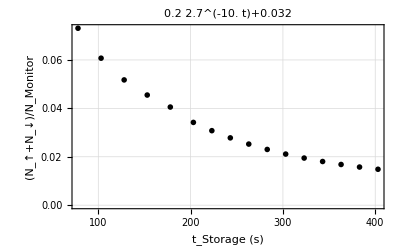

NonlinearModelFit::ivar: {-0.0691768,-0.0690388,-0.0689009,-0.068763,-0.068625,-0.0684871,-0.0683492,-0.0682112,-0.0680733,-0.0679354,-0.0677974,-0.0676595,-0.0675215,-0.0673836,-0.0672457,-0.0671077,-0.0669698,-0.0668319,-0.0666939,-0.066556,-0.0664181,-0.0662801,-0.0661422,-0.0660042,-0.0658663,-0.0657284,-0.0655904,-0.0654525,-0.0653146,-0.0651766,-0.0650387,-0.0649008,-0.0647628,-0.0646249,-0.0644869,-0.064349,-0.0642111,-0.0640731,-0.0639352,-0.0637973,-0.0636593,-0.0635214,-0.0633835,-0.0632455,-0.0631076,-0.0629696,-0.0628317,-0.0626938,-0.0625558,-0.0624179,«451»} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

{4000. NonlinearModelFit[{{78,0.0731},{103,0.06073},{128,0.05175},{153,0.0455},{178,0.04054},{203,0.034198},{223,0.0307827},{243,0.0278086},{263,0.025242},{283,0.0230269},{303,0.0211152},{323,0.0194653},{343,0.0180415},{363,0.0168126},{383,0.0157521},{403,0.0148369}},{aa-0.0691768 ⅇ^(-0.0693147 tt),aa-0.0690388 ⅇ^(-0.0693147 tt),aa-0.0689009 ⅇ^(-0.0693147 tt),aa-0.068763 ⅇ^(-0.0693147 tt),aa-0.068625 ⅇ^(-0.0693147 tt),aa-0.0684871 ⅇ^(-0.0693147 tt),aa-0.0683492 ⅇ^(-0.0693147 tt),aa-0.0682112 ⅇ^(-0.0693147 tt),486,aa-0.00103626 ⅇ^(-0.0693147 tt),aa-0.000898319 ⅇ^(-0.0693147 tt),aa-0.000760382 ⅇ^(-0.0693147 tt),aa-0.000622446 ⅇ^(-0.0693147 tt),aa-0.00048451 ⅇ^(-0.0693147 tt),aa-0.000346574 ⅇ^(-0.0693147 tt),aa-0.000208637 ⅇ^(-0.0693147 tt)},{{aa,1},{{-0.0691768,499,-23},0.1}},tt][FitResiduals],14,25000. 1}
 |  |  |  |

```mathematica
fitchk=Table[NonlinearModelFit[ftallseries2,(aa+bb Exp[tt cct]),{{aa,1},{bb,.1}},tt],{cct,scnftst,scnend,scnint}];
Show[{
EDAListPlot[ptallseries2,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel->SetPrecision[nlm2["BestFit"],2],PlotMarkers->{Red,Medium}],
Plot[Table[fitchk[[k]][xx],{k,1,Dimensions[fitchk][[1]]}],{xx,10,420},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]}}]
}]
fitchk[[1]]["FitResiduals"]/errallseries2
```

```mathematica
st=10;
st2=-1/st
end=1000;
end2=-1/end
1/Table[(1/k),{k,st2,end2,.001}]
```

-1/10

-1/1000

{-0.1,-0.099,-0.098,-0.097,-0.096,-0.095,-0.094,-0.093,-0.092,-0.091,-0.09,-0.089,-0.088,-0.087,-0.086,-0.085,-0.084,-0.083,-0.082,-0.081,-0.08,-0.079,-0.078,-0.077,-0.076,-0.075,-0.074,-0.073,-0.072,-0.071,-0.07,-0.069,-0.068,-0.067,-0.066,-0.065,-0.064,-0.063,-0.062,-0.061,-0.06,-0.059,-0.058,-0.057,-0.056,-0.055,-0.054,-0.053,-0.052,-0.051,-0.05,-0.049,-0.048,-0.047,-0.046,-0.045,-0.044,-0.043,-0.042,-0.041,-0.04,-0.039,-0.038,-0.037,-0.036,-0.035,-0.034,-0.033,-0.032,-0.031,-0.03,-0.029,-0.028,-0.027,-0.026,-0.025,-0.024,-0.023,-0.022,-0.021,-0.02,-0.019,-0.018,-0.017,-0.016,-0.015,-0.014,-0.013,-0.012,-0.011,-0.01,-0.009,-0.008,-0.007,-0.006,-0.005,-0.004,-0.003,-0.002,-0.001}

```mathematica
Export["errallseries3.dat",errallseries3]
Export["ptallseries3.dat",ptallseries3]
Export["ftallseries3.dat",ftallseries3]
```

errallseries3.dat

ptallseries3.dat

ftallseries3.dat

```mathematica
ftallseries3
ftallseries3=Import[StringJoin[curDir,"//","ftallseries3.dat"]]
```

{{78,0.0731},{103,0.06073},{128,0.05175},{153,0.0455},{178,0.04054},{203,0.034198},{223,0.0307827},{243,0.0278086},{263,0.025242},{283,0.0230269},{303,0.0211152},{323,0.0194653},{343,0.0180415},{363,0.0168126},{383,0.0157521},{403,0.0148369}}

{{78,0.0731},{103,0.06073},{128,0.05175},{153,0.0455},{178,0.04054},{203,0.034198},{223,0.0307827},{243,0.0278086},{263,0.025242},{283,0.0230269},{303,0.0211152},{323,0.0194653},{343,0.0180415},{363,0.0168126},{383,0.0157521},{403,0.0148369}}

```mathematica
errallseries3
```

{0.00025,0.00022,0.00025,0.00023,0.0002,0.000041,0.0000477744,0.0000463947,0.0000453266,0.0000467143,0.0000498346,0.0000551748,0.0000425447,0.0000425206,0.0000449407,0.00004}